```mathematica
ValFibonmMinus1 = Import["m-1DislocationIrrationalEnergies.dat"];
```

```mathematica
ValFibonmPlus1= Import["m+1DislocationIrrationalEnergies.dat"];
```

```mathematica
ValFibonmMinus3 = Import["m+3DislocationIrrationalEnergies.dat"];
```

```mathematica
ValFibonmPlus3 = Import["m-3DislocationIrrationalEnergies.dat"];
```

```mathematica
Midpt = Dimensions[ValFibonmMinus1][[1]]/2
```

84

```mathematica
ValFibonmMinus1[[Midpt]]
```

{84,-7.50233×10^-8}

```mathematica
Append[ValFibonmMinus1[[Midpt]],{11,3}]
```

{84,-7.50233×10^-8,{11,3}}

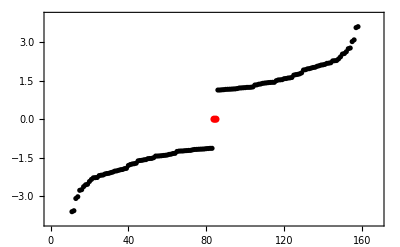

```mathematica
A1 = Show[ListPlot[ValFibonmMinus1 ,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black,PlotRange->{All,{-4,4}}],
ListPlot[Append[{ValFibonmMinus1[[Midpt]]},ValFibonmMinus1[[Midpt+1]]],PlotStyle-> Red]]
```

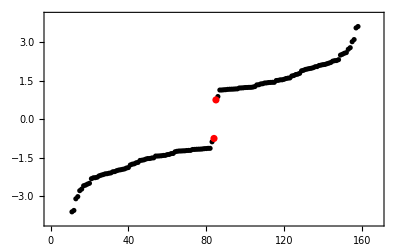

```mathematica
A2 = Show[ListPlot[ValFibonmPlus1 ,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black,PlotRange->{All,{-4,4}}],
ListPlot[Append[{ValFibonmPlus1[[Midpt]]},ValFibonmPlus1[[Midpt+1]]],PlotStyle-> Red]]
```

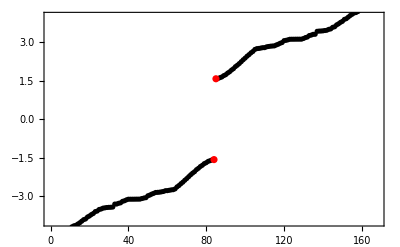

```mathematica
A3 = Show[ListPlot[ValFibonmMinus3 ,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black,PlotRange->{All,{-4,4}}],
ListPlot[Append[{ValFibonmMinus3[[Midpt]]},ValFibonmMinus3[[Midpt+1]]],PlotStyle-> Red]]
```

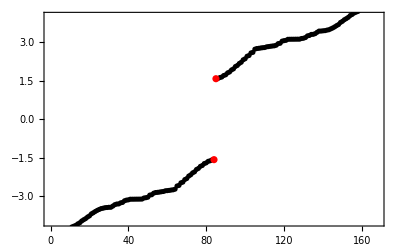

```mathematica
A4 = Show[ListPlot[ValFibonmPlus3 ,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black,PlotRange->{All,{-4,4}}],
ListPlot[Append[{ValFibonmPlus3[[Midpt]]},ValFibonmPlus3[[Midpt+1]]],PlotStyle-> Red]]
```